### Problem 5-39(v) we all had attempted and had trouble proving in class looks like this:

```mathematica
f[x_]:=Sqrt[x^2+2x]-x
```

Demand that epsilon=0.001.

```mathematica
epsilon=0.001
```

0.001

That means that this thing has to be between 0.999 and 1.001.

I claim that N=1/epsilon=1000 is sufficient.

Let’s check by choosing an x>1000, like 1001:

```mathematica
f[1001.0]
```

0.999501

It worked! In fact, it is within 0.0005 of 1.

Also here is a graph of the function out to x=1000.

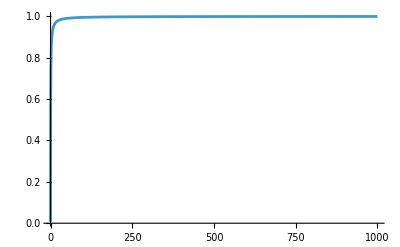

```mathematica
Plot[f[x],{x,0,1000},PlotRange->All]
```